# Лабораторная работа 3.

Шпак Андрей, 3 курс, 5 группа.

## Задание 1. Математический маятник под действием силы тяжести без учета сопротивления среды.

```mathematica
g=QuantityMagnitude@WolframAlpha["Gravitational acceleration value", {{"Value",1},"QuantityData"}]
```

9.807

### Задание 1.1 (Фазовый портрет)

```mathematica
(*Фото*)
```

```mathematica
l=1;
```

```mathematica
legend=LineLegend[{Red,Blue,Green,Yellow},{"Сепаратриса","Вращательное движение","Колебательное движение","Нижнее положение равновесия"}];
```

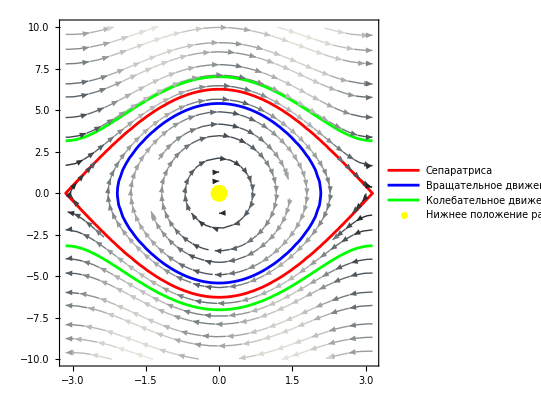

```mathematica
Show[StreamPlot[{ω,-g/l*Sin[α]},{α,-Pi,Pi},{ω,-10,10},StreamColorFunction->"GrayTones"],ContourPlot[ω^2/2-g/l*Cos[α]==g/l,{α,-Pi,Pi},{ω,-10,10},ContourStyle->{Red,Thick},PlotLegends->{"Сепаратриса"}],
ContourPlot[ω^2/2-g/l*Cos[α]+5==g/l,{α,-Pi,Pi},{ω,-10,10},ContourStyle->{Blue,Thick},PlotLegends->{"Вращательное движение"}],
ContourPlot[ω^2/2-g/l*Cos[α]-5==g/l,{α,-Pi,Pi},{ω,-10,10},ContourStyle->{Green,Thick},PlotLegends->{"Колебательное движение"}],
ListPlot[{{0,0}},PlotStyle->{PointSize[0.03],Yellow},PlotLegends->{"Нижнее положение равновесия"}],PlotRange->All,PlotLegends->Placed[{"Сепаратриса","Вращательное движение","Колебательное движение","Нижнее положение равновесия"},{Right,Top}]]
```